# Trapped-Ions Oxford/Hub virtual device

Set environment, such as threads, gpu, etc.

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"8"]
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink

```mathematica
Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_cpu_develop"];
```

Virtual quantum devices, loaded after questlink

```mathematica
Get["../vqd.wl"]
```

Time unit : μs
Frequency unit: MHz

```mathematica
Options[TrappedIonOxford]={
(*the nodes name together with the total qubits on each node*)
Nodes-><|"Alice"->4,"Bob"->4|>,
(* time and duration unit μs: 300 ms*)
T1-><|"Alice"->3*10^5, "Bob"->3*10^5    |>,
(* Simulating T2* error by gaussian decay: 10 ms *)
T2s-><|"Alice"->10^4,  "Bob"->10^4   |>,
(* Switch on/off the standard passive noise: Amplitude damping T1 and dephasing T2  *)
StdPassiveNoise->True,
(* Duration for moving operations: Split, Combine, and physical swap; they have zero error *)
DurMove-><|"Alice"-> <|Shutl->10, Splz->50, Comb->50, SWAPLoc->10 |>,"Bob"-><|Shutl->10, Splz->50, Comb->50, SWAPLoc->10 |>|>,
(* fidelity of preparation/initialisation; initialisation is done by amplitude damping *)
FidInit-><|"Alice"->0.9999, "Bob"->0.9998|>,
DurInit-><|"Alice"->20,"Bob"->20|>,

(* Readout error includes bitflip and scattering
Bitflip error represents symmetric error on both 0 and 1 readout  
Amplitude damping represents scattering error affecting the neighborhood qubits (in the same zone): collapsing the superposition into 0
*)
DurRead-><|"Alice"->20, "Bob"->20|>,
BFProb-><|"Alice"->10^-3,"Bob"->10^-3|>,
ScatProb-><|"Alice"->0.05, "Bob"->0.05|>,

(*Fidelity of single x- and y- rotations; z-rotation is instaneous (noiseless, virtual)
future:Set manually the error coefficient instead of setting the fidelity at the first place.
Future: off-resonant oscillation in the same zone*)
FidSingleXY-><|"Alice"->0.99999, "Bob"->0.99999|>,
(*fraction of depolarising:dephasing noise of the x- and y- rotations *)
EFSingleXY-><|"Alice"->{0,1},"Bob"->{0,1}|>,

(* Frequency unit is MHz *)
(* Rabi frequency on single rotations in MHz  *)
RabiFreq-><|"Alice"->1, "Bob"->1 |>,
(* Frequency of CZ operation*)
FreqCZ-><|"Alice"->0.1,"Bob"->0.1|>,
(*Fidelity of controlled-Z operation *)
FidCZ-><|"Alice"->0.999, "Bob"->0.999|>,
EFCZ-><|"Alice"->{1,0},"Bob"->{1,0}|>,
(* frequency of remote entanglement MHz *)
FreqEnt->100*10^3,
(* fidelity of remote entanglement *)
FidEnt->0.985,
(* fraction of noise: depolarizing:dephasing *)
EFEnt->{0.2,0.8}
};
```

Commonly defined standard gates that can be easily composed to the native Trapped ion gates , chart style

```mathematica
StdGates::usage="Replacements for standard gates that are straightforwardly composable to the native trapped ions gates. Here, hadamard is implemented with π/2-rotation around";
StdGates={Subscript[H, q_][n_]:>Sequence@@{Subscript[Rx, q][n,π/2]}};
chartstyle[label_]:={ImageSize->400,BarSpacing->0.1,ColorFunction->Function[{height},If[height<0.1,ColorData["Rainbow"][10height],ColorData["DeepSeaColors"][(height-0.9)*10]]],ChartElementFunction->"Cube",ChartStyle->EdgeForm[Thick],PlotTheme->"Business",Ticks->{{{1,"00"},{2,"01"},{3,"10"},{4,"11"}},{{1,"00"},{2,"01"},{3,"10"},{4,"11"}},Automatic},LabelStyle->Directive[Bold,Black],
Epilog->Inset[Style[label,Thick,17],ImageScaled[{.2,.7}]],PlotRange->All
};
```

[Native Gates]
 Init_q[node], Read_q[node], Rx_q[node,θ], Ry_q[node,θ], CZ_(q1,q2)[node], Ent[node1, node2], SWAPLoc_(q1,q2)[node], Splz_(q1,q2)[node,zone_destination], Comb_(q1,q2)[node], Comb_(q1,q2)[node,zone_destination]

[Zone and operations]
[from notes]
Zone 1 : prepare, store?, detect
Zone 2 : prepare, store?, detect, logic
Zone 3 : prepare, store?, detect, logic
Zone 4 : remote entangle
[from email]
    a. Zone 1 supports prep, detect, split, combine and rotate (SWAP), but
        no local or remote quantum logic
     b. Zone 2 and 3 are as (a) plus local logic (1Q and 2Q) only
     c. Zone 4 supports remote logic only (no split, combine, rotate?)

The device initialised with a connected ions in the zone 1.

```mathematica
dev=TrappedIonOxford[];
dev@ShowNodes
```

Alice | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Bob | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Export["~/vqd/img/tions.pdf",%]
```

~/vqd/img/tions.pdf

The total circuit and moves until page 38. The expected result is qubit 4 at zone 2 is highly entangled after 3 distillations .

```mathematica
circ={Subscript[Splz, 2,3]["Alice",3],Subscript[Splz, 2,3]["Bob",3],Subscript[Init, 3]["Alice"],Subscript[Init, 4]["Alice"],Subscript[Init, 3]["Bob"],Subscript[Init, 4]["Bob"],Subscript[Splz, 3,4]["Alice",4],Subscript[Splz, 3,4]["Bob",4],Subscript[Ent, 4,4]["Alice","Bob"],Subscript[Comb, 3,4]["Alice",3],Subscript[Comb, 3,4]["Bob",3],Subscript[SWAPLoc, 3,4]["Alice"],Subscript[SWAPLoc, 3,4]["Bob"],Subscript[Splz, 4,3]["Alice",4],Subscript[Splz, 4,3]["Bob",4],Subscript[Ent, 3,3]["Alice","Bob"],Subscript[Comb, 4,3]["Alice",3],Subscript[Comb, 4,3]["Bob",3],Subscript[CZ, 4,3]["Alice"],Subscript[CZ, 4,3]["Bob"],Subscript[Splz, 4,3]["Alice",2],Subscript[Splz, 4,3]["Bob",2],Subscript[Init, 1]["Alice"],Subscript[Init, 1]["Bob"],Subscript[Read, 3]["Alice"],Subscript[Read, 3]["Bob"],Subscript[Splz, 1,2]["Alice",2],Subscript[Splz, 1,2]["Bob",2],Subscript[Init, 3]["Alice"],Subscript[Init, 3]["Bob"],Subscript[Comb, 2,4]["Alice"],Subscript[Comb, 2,4]["Bob"],Subscript[Shutl, 3]["Alice",4],Subscript[Shutl, 3]["Bob",4],Subscript[Ent, 3,3]["Alice","Bob"],Subscript[SWAPLoc, 2,4]["Alice"],Subscript[SWAPLoc, 2,4]["Bob"],Subscript[Splz, 4,2]["Alice",3],Subscript[Splz, 4,2]["Bob",3],Subscript[Comb, 2,3]["Alice",3],Subscript[Comb, 2,3]["Bob",3],Subscript[SWAPLoc, 2,3]["Alice"],Subscript[SWAPLoc, 2,3]["Bob"],Subscript[Splz, 3,2]["Alice",4],Subscript[Splz, 3,2]["Bob",4],
Subscript[Ent, 2,2]["Alice","Bob"],Subscript[Comb, 3,2]["Alice",3],Subscript[Comb, 3,2]["Bob",3],Subscript[CZ, 3,2]["Alice"],Subscript[CZ, 3,2]["Bob"],Subscript[Splz, 3,2]["Alice",2],Subscript[Splz, 3,2]["Bob",2],Subscript[Comb, 4,3]["Alice"],Subscript[CZ, 4,3]["Alice"],Subscript[Comb, 4,3]["Bob"],Subscript[CZ, 4,3]["Bob"],Subscript[Read, 2]["Alice"],Subscript[Read, 2]["Bob"],Subscript[H, 4]["Alice"],Subscript[H, 3]["Alice"],Subscript[H, 3]["Bob"],Subscript[H, 4]["Bob"],Subscript[CZ, 4,3]["Alice"],Subscript[CZ, 4,3]["Bob"],Subscript[Shutl, 2]["Alice",4],Subscript[Shutl, 2]["Bob",4],Subscript[Splz, 4,3]["Alice",3],Subscript[Splz, 4,3]["Bob",3]
}/.StdGates;
```

Check the arrangement of the circuit in the total density matrix. Here is completely serial within a node.
 It does not update the device state, thus we cannot check the final position of ions.

```mathematica
(*DrawCircuit@CircTrappedIons[circ,dev]*)
```

This will show the total scheduling, noise operation, and the final form in the simulation.
Set the MapQubits->False and ReplaceAliases->True if you intended to do the density matrix simulation

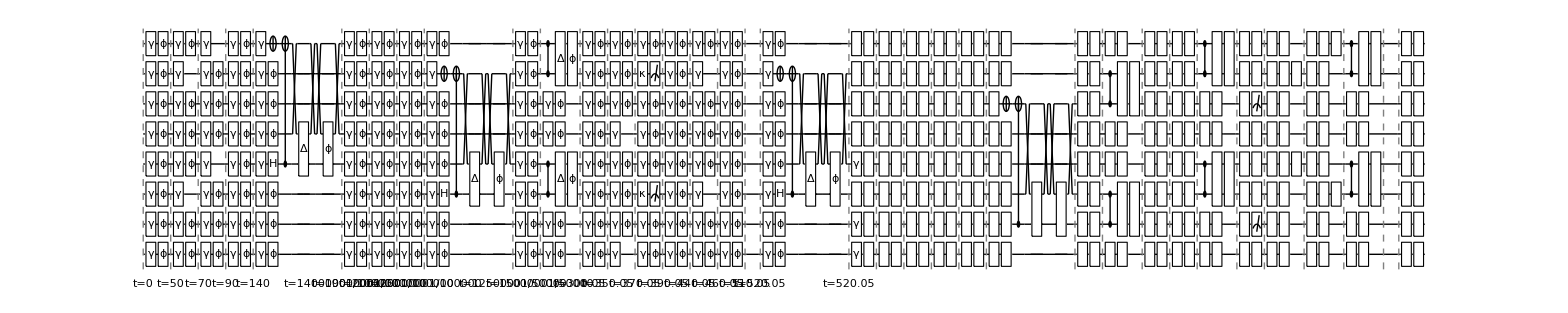

```mathematica
dev=TrappedIonOxford[];
circ2=CircTrappedIons[circ,dev,MapQubits->False];
noisycirc=InsertCircuitNoise[circ2,dev, ReplaceAliases->True];
DrawCircuit[%,8]
```

```mathematica
(* initialise the qubit with random mixed state, then apply the noisy circuit *)
DestroyAllQuregs[];
ρ=CreateDensityQureg[8];
ψ2=CreateQureg[2];
ρ2=CreateDensityQureg[2];
SetQuregMatrix[ρ,RandomMixState[8]];
ApplyCircuit[ρ,ExtractCircuit@noisycirc];
ApplyCircuit[InitZeroState@ψ2,{Subscript[H, 0],Subscript[C, 0][Subscript[X, 1]]}];
SetQuregMatrix[ρ2,PartialTrace[ρ,0,1,2,4,5,6]];
CalcFidelity[ρ2,ψ2]
PlotDensityMatrix[PartialTrace[ρ,0,1,2,4,5,6],ψ2,Sequence@@chartstyle[""]]
```

0.963685

-Graphics3D-

Recall the expected result is qubit 4 at zone 2 is highly entangled after 3 distillations: trace out the rest except qubit 4 at both nodes. Thus we trace out the rest of other qubits above.

```mathematica
dev@ShowNodes
```

Alice | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Bob | -Graphics- | -Graphics- | -Graphics- | -Graphics-

[FUTURE FEATURES]

T1, and T2 for individual qubits
T1-><|”Alice”-><|1->100,2->101|>, “Bob”->110 |>,
ModifyDev[dev,Opts->xxx]. One can modify T1, T2 in between.
Passive noise different on each zone.
The noise on the move operations? (passive noise)
Correlated noise happens only to qubits with the same zone.
The role of measurement/outcome in the sequence?
Measurement involves scattering that can affect neighborhood atoms within raidus.
Parrallel -> False (done), Default (no operations in the same zone, always parallel Alice and Bob, Ent is always serial) , Full (Default+ parallel when in different zone)

## Entanglement distillation against majority dephasing noise

In the case when entanglement has only dephasing errors, one-round of distillation is sufficient.

```mathematica
bell::usage="return circuit that gives bell state";
```

```mathematica
Subscript[bell, p_,q_]:=Sequence@@{Subscript[H, p],Subscript[X, q],Subscript[C, p][Subscript[X, q]]}
Subscript[belle, p_,q_][fid_,entnoise_]:=With[{ef=VQD`Private`entfid2DepolDeph[fid,entnoise,FidEnt]},Sequence@@{Subscript[bell, p,q],Subscript[Depol, p,q][ef[[1]]],Subscript[Deph, p,q][ef[[2]]]}];

distill::usage="distill[nrounds]. show n-rounds of ent distillation.";
distill[n_,fid_,ef_]:=Flatten@{Subscript[bellerr, 0,2][fid,ef],ConstantArray[{Subscript[bellerr, 1,3][fid,ef],Subscript[H, 0],Subscript[H, 1],Subscript[H, 2],Subscript[H, 3],Subscript[C, 0][Subscript[X, 1]],Subscript[C, 2][Subscript[X, 3]],Subscript[Rx, 2][π],Subscript[M, 1],Subscript[M, 3]},n]};

distill2[n_,fid_,ef_]:=Module[{circ={}},
AppendTo[circ,Subscript[bellerr, 0,2][fid,ef]];
If[n==0, Return@circ];
Table[
(*alternatively distill the bitflip and dephasing*)
If[OddQ@round,
AppendTo[circ,{Subscript[bellerr, 1,3][fid,ef],Subscript[H, 0],Subscript[H, 1],Subscript[H, 2],Subscript[H, 3],Subscript[C, 0][Subscript[X, 1]],Subscript[C, 2][Subscript[X, 3]],Subscript[Rx, 2][π],Subscript[M, 1],Subscript[M, 3]}]
,
AppendTo[circ,{Subscript[bellerr, 1,3][fid,ef],Subscript[C, 0][Subscript[X, 1]],Subscript[C, 2][Subscript[X, 3]],Subscript[M, 1],Subscript[M, 3]}]
]
,{round,n}];
Flatten[circ]
]

gatereplace={Subscript[H, q_]:>Sequence@@{Subscript[Ry, q][π/2],Subscript[Rx, q][-π]},Subscript[bellerr, p_,q_][a___]:>Subscript[belle, p,q][a]}; 
wrap[l_]:=Transpose@{l[[All,1]],l[[All,3]]}
```

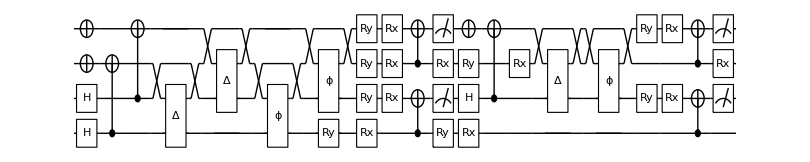

```mathematica
DrawCircuit[distill[2,0.9,{0,1}]/.gatereplace]
```

```mathematica
DrawCircuit[distill[2,0.9,{0,1}]/.gatereplace]
```

-Graphics-

```mathematica
SetAttributes[DistillDephasing,HoldAll]
DistillDephasing::usage="DistillDephasing[nrounds,fident,error_fraction,ρ,ρ2,ψ2]. Disillation on dephasing errors";
DistillDephasing[nrounds_,fident_,errfrac_,ρ_,ρ2_,ψ2_,both_:False]:=Module[{trial,out,fid},
ApplyCircuit[InitZeroState@ψ2,{Subscript[bell, 0,1]}];
trial=0;
While[True,
trial++;
out=If[both,
Flatten@ApplyCircuit[InitZeroState@ρ,distill2[nrounds,fident,errfrac]/.gatereplace]
,
Flatten@ApplyCircuit[InitZeroState@ρ,distill[nrounds,fident,errfrac]/.gatereplace]
];
If[AllTrue[out,#==0&] (* omit output 11, avoding conditional correction XX *),
SetQuregMatrix[ρ2,PartialTrace[ρ,1,3]];
Break[]]
];
fid=100*CalcFidelity[ρ2,ψ2];
{nrounds, trial,fid}
]
```

```mathematica
DestroyAllQuregs[];
ρ=CreateDensityQureg[4];
ρ2=CreateDensityQureg[2];
ψ2=CreateQureg[2];
```

Fully dephasing vs a little bit depolarising

```mathematica
OptionValue[TrappedIonOxford,FidEnt]
```

0.985

```mathematica
fidEnt=0.985; (* entanglement fidelity *)
efnoise={0,1.0}; (* fraction of entnglement noise depol:deph *)
```

```mathematica
DistillDephasing[2,fidEnt,{0.1,0.9},ρ,ρ2,ψ2]
```

{2,2,99.9187}

```mathematica
(* Dephasing distillation. Returns {nround, ntrial, fidelity}  *)
res1=Table[DistillDephasing[round,fidEnt,{0.1,0.9},ρ,ρ2,ψ2],{round,0,8}]
res2=Table[DistillDephasing[round,fidEnt,{0.9,0.1},ρ,ρ2,ψ2],{round,0,8}]

(* Deph and bitflip distillation. Returns {nround, ntrial, fidelity}  *)
res12=Table[DistillDephasing[round,fidEnt,{0.1,0.9},ρ,ρ2,ψ2,True],{round,0,8}]
res22=Table[DistillDephasing[round,fidEnt,{0.9,0.1},ρ,ρ2,ψ2,True],{round,0,8}]
```

{{0,1,98.5},{1,3,99.8591},{2,2,99.9187},{3,10,99.9373},{4,4,99.9382},{5,141,99.9384},{6,85,99.9385},{7,162,99.9385},{8,361,99.9385}}

{{0,1,98.5},{1,1,99.067},{2,1,99.5214},{3,24,99.5264},{4,43,99.5291},{5,15,99.5291},{6,5,99.5292},{7,72,99.5292},{8,30,99.5292}}

{{0,1,98.5},{1,2,99.8591},{2,8,98.5},{3,5,99.9179},{4,2,98.5581},{5,8,99.9188},{6,151,98.5581},{7,353,99.9188},{8,24,98.5581}}

{{0,1,98.5},{1,5,99.067},{2,6,98.5},{3,5,99.5208},{4,10,98.9534},{5,31,99.5257},{6,5,98.9534},{7,54,99.5257},{8,247,98.9534}}

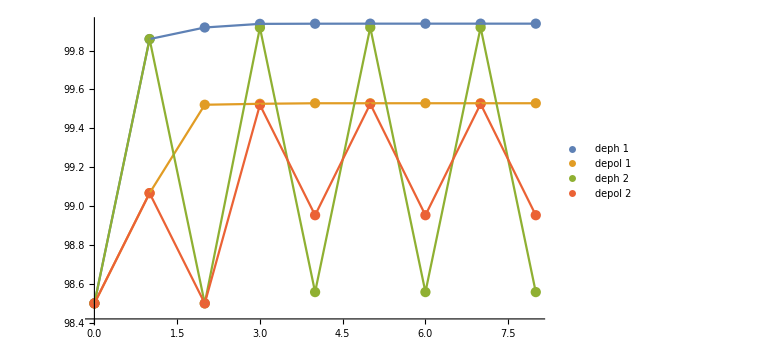

```mathematica
Show[
ListPlot[wrap/@{res1,res2,res12,res22},PlotRange->All,PlotLegends->{"deph 1","depol 1","deph 2","depol 2"}]
,
ListPlot[wrap/@{res1,res2,res12,res22},PlotRange->All,Joined->True]
,ImageSize->Large,PlotTheme->"Detailed"
]
```

## Implementation on the trapped ions

Zero, One, two-rounds of entanglement distillation

```mathematica
(* implementing distillation circuit for round 0 until round 2*)
(*DeleteCases[SimplifyCircuit[distill[1]/.{Subscript[C, p_][Subscript[X, q_]]:>Sequence@@{Subscript[H, q],Subscript[CZ, p,q],Subscript[H, q]}}],G[_]]/.{Subscript[H, q_]:>{Subscript[Ry, q][π/2],Subscript[Rx, q][-π]}}*)
distcirc=<|
0->{Subscript[Splz, 3,4]["Alice",3],Subscript[Splz, 3,4]["Bob",3],Subscript[Init, 4]["Alice"],Subscript[Init, 4]["Bob"],Subscript[Shutl, 4]["Alice",4],Subscript[Shutl, 4]["Bob",4],Subscript[Ent, 4,4]["Alice","Bob"]},
1->{Subscript[Splz, 2,3]["Alice",3],Subscript[Splz, 2,3]["Bob",3],Subscript[Init, 3]["Alice"],Subscript[Init, 4]["Alice"],Subscript[Init, 3]["Bob"],Subscript[Init, 4]["Bob"],Subscript[Splz, 3,4]["Alice",4],Subscript[Splz, 3,4]["Bob",4],Subscript[Ent, 4,4]["Alice","Bob"],Subscript[Comb, 3,4]["Alice",3],Subscript[Comb, 3,4]["Bob",3],Subscript[SWAPLoc, 3,4]["Alice"],Subscript[SWAPLoc, 3,4]["Bob"],Subscript[Splz, 4,3]["Alice",4],Subscript[Splz, 4,3]["Bob",4],Subscript[Ent, 3,3]["Alice","Bob"],
Subscript[Ry, 4]["Alice",π/2],Subscript[Rx, 4]["Alice",-π],Subscript[Ry, 4]["Bob",π/2],Subscript[Rx, 4]["Bob",-π],Subscript[Comb, 4,3]["Alice",3],Subscript[Comb, 4,3]["Bob",3],Subscript[CZ, 4,3]["Alice"],Subscript[CZ, 4,3]["Bob"],Subscript[Ry, 3]["Alice",π/2],Subscript[Rx, 3]["Alice",-π],Subscript[Ry, 3]["Bob",π/2],Subscript[Rx, 3]["Bob",-π],Subscript[Read, 3]["Alice"],Subscript[Read, 3]["Bob"],Subscript[Rx, 4]["Bob",π]
},
2->{Subscript[Splz, 2,3]["Alice",3],Subscript[Splz, 2,3]["Bob",3],Subscript[Init, 3]["Alice"],Subscript[Init, 4]["Alice"],Subscript[Init, 3]["Bob"],Subscript[Init, 4]["Bob"],Subscript[Splz, 3,4]["Alice",4],Subscript[Splz, 3,4]["Bob",4],Subscript[Ent, 4,4]["Alice","Bob"],Subscript[Comb, 3,4]["Alice",3],Subscript[Comb, 3,4]["Bob",3],Subscript[SWAPLoc, 3,4]["Alice"],Subscript[SWAPLoc, 3,4]["Bob"],Subscript[Splz, 4,3]["Alice",4],Subscript[Splz, 4,3]["Bob",4],Subscript[Ent, 3,3]["Alice","Bob"],
Subscript[Ry, 4]["Alice",π/2],Subscript[Rx, 4]["Alice",-π],Subscript[Ry, 4]["Bob",π/2],Subscript[Rx, 4]["Bob",-π],
Subscript[Comb, 4,3]["Alice",3],Subscript[Comb, 4,3]["Bob",3],Subscript[CZ, 4,3]["Alice"],Subscript[CZ, 4,3]["Bob"],
Subscript[Ry, 3]["Alice",π/2],Subscript[Rx, 3]["Alice",-π],Subscript[Ry, 4]["Alice",π/2],Subscript[Rx, 4]["Alice",-π],Subscript[Ry, 3]["Bob",π/2],Subscript[Rx, 3]["Bob",-π],Subscript[Rx, 4]["Bob",π],Subscript[Ry, 4]["Bob",π/2],Subscript[Rx, 4]["Bob",-π],Subscript[Read, 3]["Alice"],Subscript[Read, 3]["Bob"],
Subscript[Splz, 4,3]["Alice",4],Subscript[Splz, 4,3]["Bob",4],Subscript[Ent, 3,3]["Alice","Bob"],Subscript[Comb, 4,3]["Alice",3],Subscript[Comb, 4,3]["Bob",3],
Subscript[CZ, 4,3]["Alice"],Subscript[CZ, 4,3]["Bob"],Subscript[Ry, 3]["Alice",π/2],Subscript[Rx, 3]["Alice",-π],Subscript[Ry, 3]["Bob",π/2],Subscript[Rx, 3]["Bob",-π],Subscript[Rx, 4]["Bob",π],Subscript[Read, 3]["Alice"],Subscript[Read, 3]["Bob"]
}
|>;
```

```mathematica
SetAttributes[DistillTIons,HoldAll]
DistillTIons[device_,nrounds_,ρ_,ρinit_,ρ2_,ψ2_,both_:False]:=Module[{circc,noisycirc,trial=0,fid,out},
circc=CircTrappedIons[distcirc[nrounds],device,MapQubits->False];
noisycirc=InsertCircuitNoise[circc,device, ReplaceAliases->True];
ApplyCircuit[InitZeroState@ψ2,{Subscript[bell, 0,1]}];
While[True,
trial++;
CloneQureg[ρ,ρinit];
out=Flatten@ApplyCircuit[ρ,ExtractCircuit@noisycirc];
       SetQuregMatrix[ρ2,PartialTrace[ρ,0,1,2,4,5,6]];
If[ContainsAll[{0},out],Break[]];
];
fid=100*CalcFidelity[ρ2,ψ2];
{nrounds,trial,fid}
]
```

Up to two-rounds of entanglement distillation

```mathematica
(* set the initial state to an unknown random state for every experimental emulation *)
DestroyAllQuregs[];
{ρ,ρinit}=CreateDensityQuregs[8,2];
ρ2=CreateDensityQureg[2];
ψ2=CreateQureg[2];
SetQuregMatrix[ρinit,RandomMixState[8]];
```

```mathematica
(* dominated by dephasing *)
dev=TrappedIonOxford[EFEnt->{0.1,0.9}];
resnoisy1=Table[
res=DistillTIons[dev,r,ρ,ρinit,ρ2,ψ2];
title=If[r===0,"raw entanglement",ToString[r]<>"-rounds"];
{round,trial,fid}=res;
Print@PlotDensityMatrix[ρ2,ψ2,PlotRange->{{1,4},{1,4},{0,0.5}},Sequence@@chartstyle["fid="<>ToString[fid]<>"\n"<>title]];
{round,trial,fid}
,{r,0,2}];
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
(* dominated by depolarising *)
dev=TrappedIonOxford[EFEnt->{0.9,0.1}];
resnoisy2=Table[
res=DistillTIons[dev,r,ρ,ρinit,ρ2,ψ2];
title=If[r===0,"raw entanglement",ToString[r]<>"-rounds"];
{round,trial,fid}=res;
Print@PlotDensityMatrix[ρ2,ψ2,PlotRange->{{1,4},{1,4},{0,0.5}},Sequence@@chartstyle["fid="<>ToString[fid]<>"\n"<>title]];
{round,trial,fid}
,{r,0,2}];
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
res1[[;;3]]
resnoisy1
res2[[;;3]]
resnoisy2
```

{{0,1,98.5},{1,3,99.8591},{2,2,99.9187}}

{{0,1,98.5},{1,1,99.7213},{2,1,99.7572}}

{{0,1,98.5},{1,1,99.067},{2,1,99.5214}}

{{0,1,98.5},{1,3,98.9319},{2,6,99.3609}}

```mathematica
dephs=Range[0,1,0.1]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

```mathematica
OptionValue[TrappedIonOxford,FidEnt]
```

0.985

```mathematica
(* gradually increase dephasing *)
results=Association@Table[
dev=TrappedIonOxford[EFEnt->{1-deph,deph}];
deph->Table[DistillTIons[dev,r,ρ,ρinit,ρ2,ψ2],{r,0,2}]
,{deph,dephs}];

results2=Association@Table[
dev=TrappedIonOxford[EFEnt->{1-deph,deph}];
deph->Table[DistillTIons[dev,r,ρ,ρinit,ρ2,ψ2,True],{r,0,2}]
,{deph,dephs}];
```

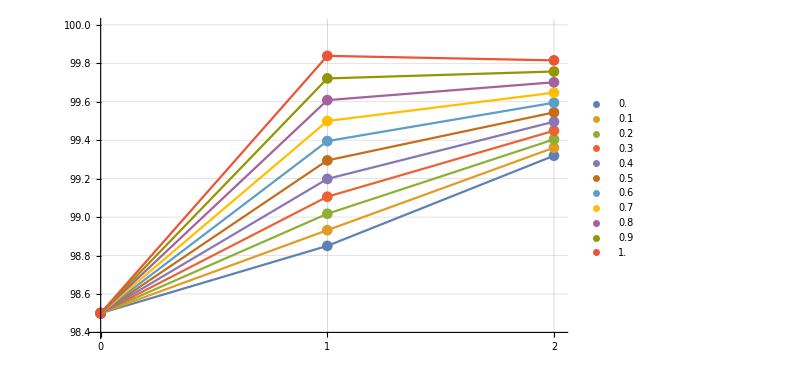

-Graphics-

```mathematica
Show[
ListPlot[Values[wrap[#]&/@results],Ticks->{{0,1,2},Automatic},GridLines->{{0,1,2},Automatic},PlotRange->{{-0.01,2.02},{98.4,100.001}},PlotLegends->Keys@results],
ListPlot[Values[wrap[#]&/@results],Joined->True,PlotRange->{{-0.01,2.02},{98.4,100.001}}]
,ImageSize->600
]

Show[
ListPlot[Values[wrap[#]&/@results2],Ticks->{{0,1,2},Automatic},GridLines->{{0,1,2},Automatic},PlotRange->{{-0.01,2.02},{98.4,100.001}},PlotLegends->Keys@results2],
ListPlot[Values[wrap[#]&/@results2],Joined->True,PlotRange->{{-0.01,2.02},{98.4,100.001}}]
,ImageSize->600
]
```